## Brian — PS 15 — 2025-04-01 — Solution

## EIWL3 Sections 37 and 38

## Exercises from EIWL3 Section 37

```mathematica
(* 37.1 *) Array[Framed[#,Background->If[EvenQ[#],Yellow,LightGray]]&,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(* 37.2 *)  Array[If[PrimeQ[#],Framed[#],#]&,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(* 37.3 *) Array[If[PrimeQ[#],Labeled[Framed[#,Background->LightGray],Mod[#,4]],#]&,100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

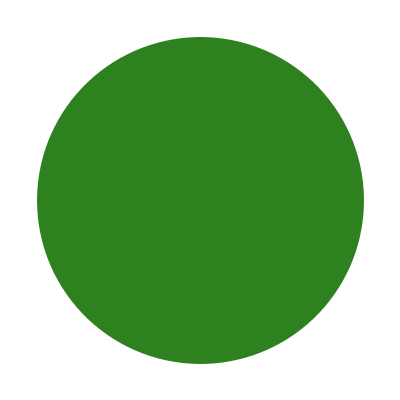

```mathematica
Graphics[{RandomColor[],Disk[]}]
```

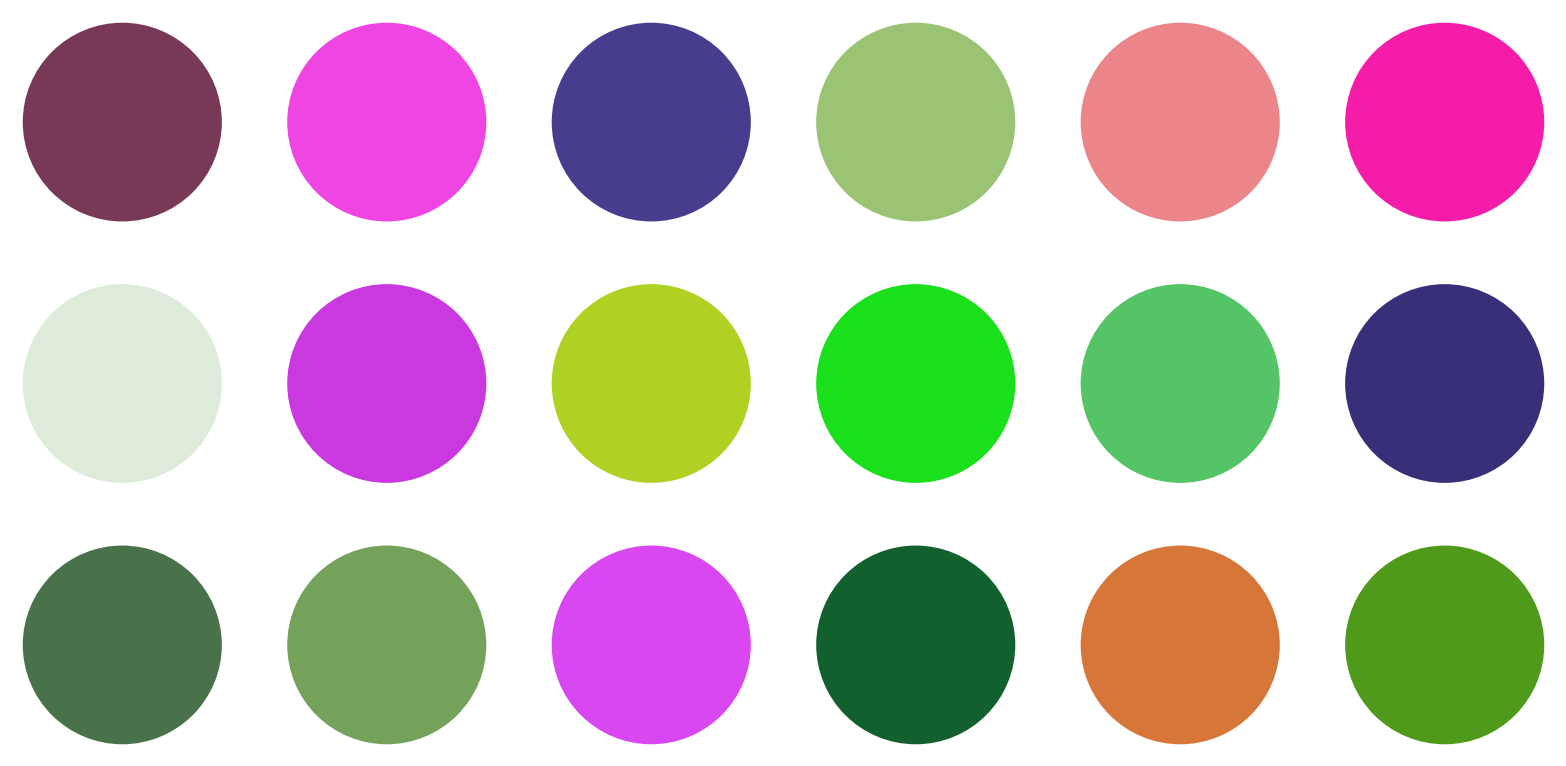

```mathematica
(* 37.4 *) GraphicsGrid[Table[Graphics[{RandomColor[],Disk[]}],3,6]]
```

```mathematica
(* 37.5 *) countries=EntityList[EntityClass["Country","GroupOf5"]];
PieChart[Labeled[#["GDP"],#]&/@countries]
```

-Graphics-

```mathematica
(* 37.6 *) 
PieChart[Labeled[#["Population"],#]&/@countries]
```

-Graphics-

```mathematica
(* 37.7 *) pieCharts = PieChart[Counts[#]]&/@Array[IntegerDigits[2^#]&,25];
GraphicsGrid[Partition[pieCharts,5]]
```

-Graphics-

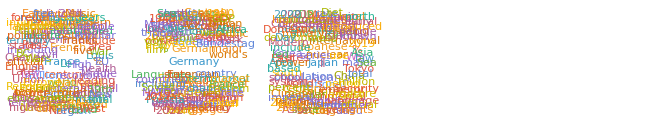

```mathematica
(* 37.8 *)
countryNames = EntityValue[countries,"Name"];
wordClouds = WordCloud[WikipediaData[#]]&/@countryNames;
GraphicsRow[wordClouds]
```

## Exercises from EIWL3 Section 38

```mathematica
(* 38.1 *)
```